```mathematica
-Graphics-;
Hlp[s_]:=1/((1+2.4114 s+3.5791 s^2)(1+0.2829 s+1.0137 s^2));
Hhp[s_]:=Hlp[1/s];
Factor[Simplify[Hhp[s]]]
LogLinearPlot[{20*Log10[Abs[Hlp[ⅈ ω]]],20*Log10[Abs[Hhp[ⅈ ω]]]},{ω,0.3,3},PlotTheme->"Monochrome",PlotLegends->{"低通","高通"},AxesLabel->{"ω_n","|A|(dB)"}]
```

(1. s^4)/((1.0137+0.2829 s+1. s^2) (3.5791+2.4114 s+1. s^2))

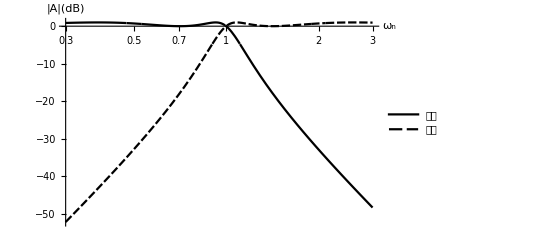

(1. s^4)/((1.+0.7654 s+1. s^2) (1.+1.8478 s+1. s^2))

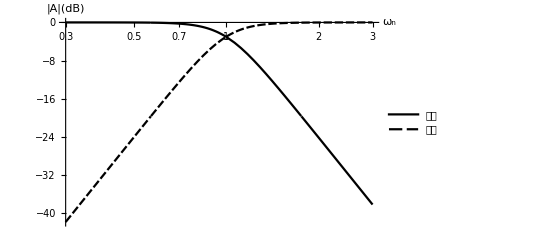

```mathematica
-Graphics-;
Hlp[s_]:=1/((1+1.8478 s+s^2)(1+0.7654 s+s^2));
Hhp[s_]:=Hlp[1/s];
Factor[Simplify[Hhp[s]]]
LogLinearPlot[{20*Log10[Abs[Hlp[ⅈ ω]]],20*Log10[Abs[Hhp[ⅈ ω]]]},{ω,0.3,3},PlotTheme->"Monochrome",PlotLegends->{"低通","高通"},AxesLabel->{"ω_n","|A|(dB)"}]
```

(0.25 s^2)/((0.69968+0.291081 s+1. s^2) (1.42922+0.416019 s+1. s^2))

(1. (1.+1. s^2)^2)/((0.69968+0.291081 s+1. s^2) (1.42922+0.416019 s+1. s^2))

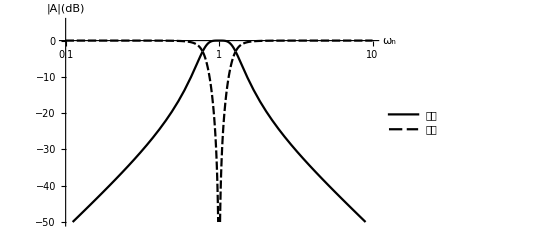

```mathematica
-Graphics-;
Hlp2[s_]:=1/(1+1.4142s+s^2);
Δω=0.5;
Hbp2[s_]:=Hlp2[1/Δω(s+1/s)];
Factor[Hbp2[s]]
Hbs2[s_]:=Hlp2[Δω/(s+1/s)];
Factor[Hbs2[s]]
LogLinearPlot[{(*20*Log10[Abs[Hlp2[ⅈ ω]]],*)20*Log10[Abs[Hbp2[ⅈ ω]]],20*Log10[Abs[Hbs2[ⅈ ω]]]},{ω,0.1,10},PlotTheme->"Monochrome",PlotLegends->{"低通","高通"},AxesLabel->{"ω_n","|A|(dB)"},PlotRange->{-50,5}]
```

```mathematica
Simplify[0.25 s^2/0.4160194970749962/0.29108050292500376]
Simplify[(1.4292248807271803+0.4160194970749962 s+1. s^2)/0.4160194970749962]
Simplify[(0.6996799548376224+0.29108050292500376 s+1. s^2)/0.29108050292500376]
```

2.06449 s^2

3.43548+1. s+2.40373 s^2

2.40373+1. s+3.43548 s^2

(0.25 s)/(1.+0.25 s+1. s^2)

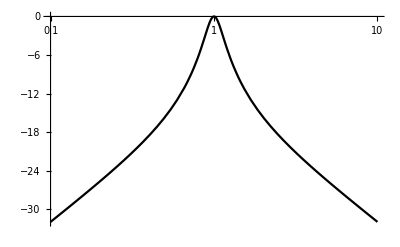

```mathematica
Hlp3[s_]:=1/(1+s);
Δω=0.25;
Hbp3[s_]:=Hlp3[1/Δω(s+1/s)];
Factor[Hbp3[s]]
LogLinearPlot[{(*20*Log10[Abs[Hlp2[ⅈ ω]]],*)20*Log10[Abs[Hbp3[ⅈ ω]]]},{ω,0.1,10},PlotTheme->"Monochrome"]
```